## Draft Computational Essay

#### Introduction

Multiway systems are systems generated by a set of rules that are recursively applied to all of the outputs.

#### Observations

Generally, with a linear or multiplicative multiway systems, merging behavior can be predicted by the various constant values.

Consider a system of the form

```mathematica
n |-> {an, n + b}
```

With this, we can predict the initial grid like pattern that arises, at least from the lower level branches.

```mathematica
Graph[With[{g=ResourceFunction["NestGraphTagged"][x|->Expand[{5x,x+3}],{n},6,"StateLabeling"->True]},Subgraph[g,First/@First[FindCycle[UndirectedGraph[g],{8}]]]]]
```

-Graphics-

where the left hand side will always have a+1 sides, and the right hand side has 2 sides, resulting in (a+3)-gons, as explained by Stephen Wolfram’s work “Multicomputation with Numbers: The Case of Simple Multiway Systems”. However, there are some exceptions to this behavior.  
For example, consider the rule set

```mathematica
n|->{2n, n+5}
```

The resulting graph ends up with one heptagon, with the remaining grids being pentagons. Every pentagon is also in the format of the generalized (n+3)-gon as explained above, which is trivial to see.

```mathematica
ResourceFunction["NestGraphTagged"][n↦{2n, n+5},{1},7,"StateLabeling"->True, PlotLegends->TraditionalForm/@{2n, n+5}]
```

-Graphics-

Zooming in on the heptagon subset, we see

```mathematica
Graph[With[{g=ResourceFunction["NestGraphTagged"][x|->Expand[{2x,x+5}],{1},6,"StateLabeling"->True]},Subgraph[g,First/@First[FindCycle[UndirectedGraph[g],{7}]]]]]
```

-Graphics-

Conveniently,

```mathematica
∃x∈Ζ^+ | a^x
```

and this can easily be seen as true, as an integer x would exist through Fermat’s Little Theorem, since a and b are relatively prime.

#### Dyck Paths

Dyck paths are lattice paths from (0, 0) to (n, n)that do not pass above the diagonal (y=x). For example, here’s an Dyck path where n=6.

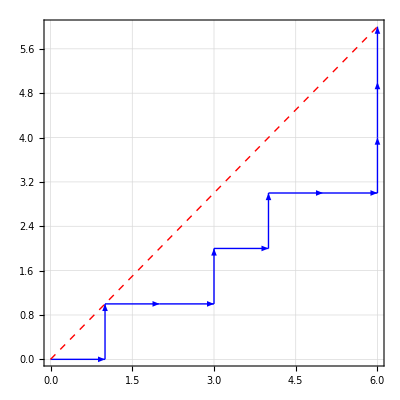

From any given point, a path can be generated by the map

```mathematica
{x, y} |-> {{x+1, y}, {x,y+1}}
```

or simply right and up “moves”. However, to make this path into a Dyck path, we will have to consider the restriction of the diagonal.

I opted to store the Dyck path by a list of the heights of the columns. For the example Dyck path above, it would be stored as

```mathematica
{0, 1, 1, 2, 3, 3, 6}
```

The 6 at the end is technically not in the graph itself, but makes the conversion graphically, which will be explained later, much less convoluted.

To turn this into a multiway graph, I recursively build the graph by finding the next edge with the rule described above.

```mathematica
dyckNext[lst_List, n_Integer] := Module[{x := Last[lst][[2]][[1]], y := Last[lst][[2]][[2]]},
	Which[
		Length[lst] == 0, {{{0, 0}, {1, 0}}},
		x==n, {{{x, y}, {x, y + 1}}},
		x > y, {{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, 
		True,{{{x, y}, {x + 1, y}}}
	]
]
```

The which above hard codes the empty set case and the ending case (i.e., all up), and checks the ending lattice point of the last edge to consider how many of the paths would be valid.

```mathematica
dyckNext[{}, 6]
dyckNext[{{{0, 0}, {1, 0}}}, 6]
dyckNext[{{{0, 0}, {1, 0}}, {{1,0},{1,1}}}, 6]
```

{{{0,0},{1,0}}}

{{{1,0},{2,0}},{{1,0},{1,1}}}

{{{1,1},{2,1}}}

This function generates the Dyck path from the list of edges provided.

```mathematica
dyckGraphDisplay[lst_List, n_Integer] := Graphics[
	{Blue, Arrow[Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[{{0, 0}, {n, n}}]}, 
	Frame -> True,
	GridLines -> Automatic,
	ImageSize -> Full
]
```

We test this, as well as a function to generate random Dyck Paths below.

```mathematica
generateDyckPath[n_Integer] := Module[{lst = {}},
	Last[
		Table[
			AppendTo[lst, RandomChoice[dyckNext[lst, n]]], {i, Range[2*n]}
		]
	]
]
```

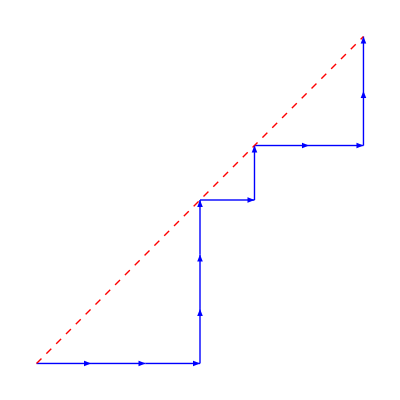

```mathematica
dyckGraph[generateDyckPath[6], 6]
```

In preparation of creating our multiway system, the display function will be updated to clear up some clutter.

```mathematica
dyckGraph[lst_List, n_Integer] := Graphics[
	{Blue, Arrow[Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[{{0, 0}, {n, n}}]}, 
	GridLines -> {Range[0, n, 1], Range[0, n, 1]},
	ImageSize -> 15
]
```

Now, to actually create the multiway system, we utilize the function “MultiwaySystem” from the Wolfram Research Repository.

```mathematica
showGraph[graphs_List, level_Integer] := ResourceFunction["MultiwaySystem"][
	<|"StateEvolutionFunction" -> Function[list, Append[list, #] & /@ dyckNext[list, n]],
	|>,
	{graphs}, level, "StatesGraph", 
	"StateRenderingFunction"->(Inset[dyckGraph[#2, n], #1]&)
]
```

and we can call it below to generate a sample Dyck path multiway system.

```mathematica
n=4
showGraph[{}, 2*n]
```

4

-Graphics-